```mathematica
A=Rectangle[{0,0},{1,1}];Clear[t,x,y];
f[x_,y_]:=Sin[2 Pi x] Abs[Sin[3 Pi y]];
g[x_,y_]:=3 Sin[Pi x] Sin[Pi y];
U=NDSolveValue[{D[u[t,x,y],{t,2}]-Inactive[Laplacian][u[t,x,y],{x,y}]==0,u[0,x,y]==f[x,y],Derivative[1,0,0][u][0,x,y]==g[x,y],DirichletCondition[u[t,x,y]==0,True]},u,{t,0,2 Pi},{x,y}∈A];
Plot3D[U[t,0.3,0.4],{t,0,1}]
Animate[ContourPlot[U[t,x,y],{x,0,1},{y,0,1}],{t,0,2Pi}]
```

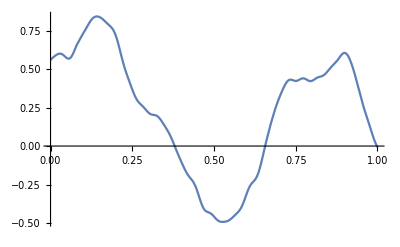

```mathematica
Plot[U[t,0.3,0.4],{t,0,1}]
```

```mathematica
f[t_,x_]:= (((1/t)^(3/2)*x*Exp[-x^2/(4 t)])/(1+Sqrt[1/t] Exp[-x^2/(4 t)]));
Simplify[ D[f[t,x],t]+f[t,x]*D[f[t,x],x]==D[f[t,x],{x,2}]]
```

True